## The Laplace Transform and Applications Section 7.5 Exercises 1(i)

t HeavisideTheta[t]

t HeavisideTheta[t]

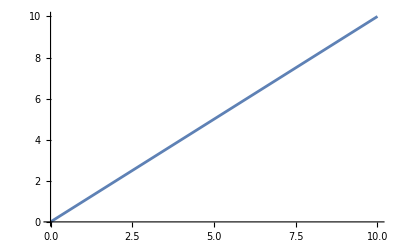

1/s^2

\left\{t \theta (t),\frac{1}{s^2}\right\}

```mathematica
f[t_]:= 1*HeavisideTheta[t]
g[t_]:= Convolve[f[x]UnitStep[x],f[x]UnitStep[x],x,t]
g[t]
Simplify[%]
plot741=Plot[g[t], {t, 0, 10}]
laplacetransform=LaplaceTransform[g[t], t,s]
TeXForm[{g[t], laplacetransform}]
(*SetDirectory[NotebookDirectory[]]
Export["7-4-1.pdf",plot741]*)
```

## 1 (ii)

```mathematica
f[t_]:= Exp[k*t]*HeavisideTheta[t]
g[t_]:= Convolve[f[x]UnitStep[x],f[x]UnitStep[x],x,t]
g[t]
Simplify[%]
(*plot741=Plot[g[t], {t, 0, 10}]*)
laplacetransform=LaplaceTransform[g[t], t,s]
TeXForm[{g[t], laplacetransform}]
(*SetDirectory[NotebookDirectory[]]
Export["7-4-1.pdf",plot741]*)
```

ⅇ^(k t) t HeavisideTheta[t]

ⅇ^(k t) t HeavisideTheta[t]

1/(k-s)^2

\left\{t \theta (t) e^{k t},\frac{1}{(k-s)^2}\right\}

## 1 (iii)

```mathematica
f[t_]:= Sin[t]*HeavisideTheta[t]
f[t]
h[t_]:= Exp[k*t]*HeavisideTheta[t]
h[t]
g[t_]:= Convolve[f[x]UnitStep[x],h[x]UnitStep[x],x,t]
g[t]
Simplify[%]
(*plot741=Plot[g[t], {t, 0, 10}]*)
laplacetransform=LaplaceTransform[g[t], t,s]
lap=Simplify[%]
TeXForm[{g[t], lap}]
(*SetDirectory[NotebookDirectory[]]
Export["7-5-3.pdf",753]*)
```

HeavisideTheta[t] Sin[t]

ⅇ^(k t) HeavisideTheta[t]

-(HeavisideTheta[t] (-ⅇ^(k t)+Cos[t]+k Sin[t]))/(1+k^2)

-(HeavisideTheta[t] (-ⅇ^(k t)+Cos[t]+k Sin[t]))/(1+k^2)

-(-1/(-k+s)+k/(1+s^2)+s/(1+s^2))/(1+k^2)

-1/((k-s) (1+s^2))

\left\{-\frac{\theta (t) \left(-e^{k t}+k \sin (t)+\cos (t)\right)}{k^2+1},-\frac{1}{\left(s^2+1\right) (k-s)}\right\}

## 1 (iv)

```mathematica
f[t_]:= Sin[ω*t]*HeavisideTheta[t]
f[t]
h[t_]:= Sin[ω*t]*HeavisideTheta[t]
h[t]
g[t_]:= Convolve[f[x]UnitStep[x],h[x]UnitStep[x],x,t]
g[t]
Simplify[%]
(*plot741=Plot[g[t], {t, 0, 10}]*)
laplacetransform=LaplaceTransform[g[t], t,s]
lap=Simplify[%]
TeXForm[{g[t], lap}]
(*SetDirectory[NotebookDirectory[]]
Export["7-5-3.pdf",753]*)
```

HeavisideTheta[t] Sin[t ω]

HeavisideTheta[t] Sin[t ω]

(HeavisideTheta[t] (-t ω Cos[t ω]+Sin[t ω]))/(2 ω)

(HeavisideTheta[t] (-t ω Cos[t ω]+Sin[t ω]))/(2 ω)

(-(ω (s^2-ω^2))/((s^2+ω^2)^2)+ω/(s^2+ω^2))/(2 ω)

ω^2/((s^2+ω^2)^2)

\left\{\frac{\theta (t) (\sin (t \omega )-t \omega  \cos (t \omega ))}{2 \omega },\frac{\omega ^2}{\left(s^2+\omega ^2\right)^2}\right\}

## 1 (v)

```mathematica
f[t_]:= Sin[ω*t]*HeavisideTheta[t]
f[t]
h[t_]:= Cos[ω*t]*HeavisideTheta[t]
h[t]
g[t_]:= Convolve[f[x]UnitStep[x],h[x]UnitStep[x],x,t]
g[t]
Simplify[%]
(*plot741=Plot[g[t], {t, 0, 10}]*)
laplacetransform=LaplaceTransform[g[t], t,s]
lap=Simplify[%]
TeXForm[{g[t], lap}]
(*SetDirectory[NotebookDirectory[]]
Export["7-5-3.pdf",753]*)
```

HeavisideTheta[t] Sin[t ω]

Cos[t ω] HeavisideTheta[t]

1/2 t HeavisideTheta[t] Sin[t ω]

1/2 t HeavisideTheta[t] Sin[t ω]

(s ω)/((s^2+ω^2)^2)

(s ω)/((s^2+ω^2)^2)

\left\{\frac{1}{2} t \theta (t) \sin (t \omega ),\frac{s \omega }{\left(s^2+\omega ^2\right)^2}\right\}

## 2. Left as an exercise 3(i)

```mathematica
f[x_]:=1*HeavisideTheta[x]
g[x_]:=x*HeavisideTheta[x]
h[x_]:=x^2*HeavisideTheta[x]
c[y_]:= Convolve[f[x], g[x],x, y]
c[y]
k[t_]:=Convolve[c[y], h[y]*HeavisideTheta[y],y, t]
k[t]
L[s_]:=LaplaceTransform[k[t], t, s]
L[s]
TeXForm[{L[s], k[t]}]
```

1/2 y^2 HeavisideTheta[y]

1/60 t^5 HeavisideTheta[t]

2/s^6

\left\{\frac{2}{s^6},\frac{t^5 \theta (t)}{60}\right\}

## 3 (ii)

```mathematica
f[x_]:=1*HeavisideTheta[x]
g[x_]:=x^2*HeavisideTheta[x]
h[x_]:=Sin[x]*HeavisideTheta[x]
c[y_]:= Convolve[f[x], g[x],x, y]
c[y]
k[t_]:=Convolve[c[y], h[y]*HeavisideTheta[y],y, t]
k[t]
L[s_]:=LaplaceTransform[k[t], t, s]
L[s]
TeXForm[{L[s], k[t]}]
```

1/3 y^3 HeavisideTheta[y]

1/3 HeavisideTheta[t] (-6 t+t^3+6 Sin[t])

1/3 (6/s^4-6/s^2+6/(1+s^2))

\left\{\frac{1}{3} \left(\frac{6}{s^4}-\frac{6}{s^2}+\frac{6}{s^2+1}\right),\frac{1}{3} \theta (t) \left(t^3-6 t+6 \sin (t)\right)\right\}

## 3 (iii)

```mathematica
f[x_]:=1*HeavisideTheta[x]
g[x_]:=Cos[x]*HeavisideTheta[x]
h[x_]:=Sin[x]*HeavisideTheta[x]
c[y_]:= Convolve[f[x], g[x],x, y]
c[y]
k[t_]:=Convolve[c[y], h[y]*HeavisideTheta[y],y, t]
k[t]
L[s_]:=LaplaceTransform[k[t], t, s]
L[s]
TeXForm[{L[s], k[t]}]
```

HeavisideTheta[y] Sin[y]

1/2 HeavisideTheta[t] (-t Cos[t]+Sin[t])

1/2 (-(-1+s^2)/((1+s^2)^2)+1/(1+s^2))

\left\{\frac{1}{2} \left(\frac{1}{s^2+1}-\frac{s^2-1}{\left(s^2+1\right)^2}\right),\frac{1}{2} \theta (t) (\sin (t)-t \cos (t))\right\}

## 3 (iv)

```mathematica
f[x_]:=1*HeavisideTheta[x]
g[x_]:=Sin[x]*HeavisideTheta[x]
h[x_]:=HeavisideTheta[x-2]*HeavisideTheta[x]
c[y_]:= Convolve[f[x], g[x],x, y]
c[y]
k[t_]:=Convolve[c[y], h[y]*HeavisideTheta[y],y, t]
k[t]
L[s_]:= Simplify[LaplaceTransform[k[t], t, s]]
L[s]
TeXForm[{L[s], k[t]}]
```

-((-1+Cos[y]) HeavisideTheta[y])

HeavisideTheta[-2+t] (-2+t+Sin[2-t])

ⅇ^(-2 s)/(s^2+s^4)

\left\{\frac{e^{-2 s}}{s^4+s^2},\theta (t-2) (t+\sin (2-t)-2)\right\}

## 3 (v)

```mathematica
f[x_]:=1*HeavisideTheta[x]
g[x_]:=HeavisideTheta[x-2]*HeavisideTheta[x]
h[x_]:=HeavisideTheta[x-4]*HeavisideTheta[x]
c[y_]:= Convolve[f[x], g[x],x, y]
c[y]
k[t_]:=Convolve[c[y], h[y]*HeavisideTheta[y],y, t]
k[t]
L[s_]:= Simplify[LaplaceTransform[k[t], t, s]]
L[s]
TeXForm[{L[s], k[t]}]
```

(-2+y) HeavisideTheta[-2+y]

1/2 (-6+t)^2 HeavisideTheta[-6+t]

ⅇ^(-6 s)/s^3

\left\{\frac{e^{-6 s}}{s^3},\frac{1}{2} (t-6)^2 \theta (t-6)\right\}

# 3 (vi)

```mathematica
h[t_]:=∫_0^t Exp[u]ⅆu
h[t]
LaplaceTransform[h[t],t, s]
Simplify[%]
TeXForm[%]
```

-1+ⅇ^t

1/(-1+s)-1/s

1/((-1+s) s)

\frac{1}{(s-1) s}

## 3 (vii)

```mathematica
h[t_]:=∫_0^t Sin[u]ⅆu
h[t]
LaplaceTransform[h[t],t, s]
Simplify[%]
TeXForm[%]
```

1-Cos[t]

1/(s+s^3)

1/(s+s^3)

\frac{1}{s^3+s}

## 3 (viii)

```mathematica
h[t_]:=∫_0^t u*Sin[u]ⅆu
h[t]
LaplaceTransform[h[t],t, s]
Simplify[%]
TeXForm[%]
```

-t Cos[t]+Sin[t]

-(-1+s^2)/((1+s^2)^2)+1/(1+s^2)

2/((1+s^2)^2)

\frac{2}{\left(s^2+1\right)^2}

## 3 (ix)

```mathematica
h[t_]:=∫_0^t Sin[u]* Cos[t-u]ⅆu
h[t]
LaplaceTransform[h[t],t, s]
Simplify[%]
TeXForm[%]
```

1/2 t Sin[t]

s/((1+s^2)^2)

s/((1+s^2)^2)

\frac{s}{\left(s^2+1\right)^2}

## 3 (x)

```mathematica
h[t_]:=t∫_0^t Sin[u]* Cos[t-u]ⅆu
h[t]
LaplaceTransform[h[t],t, s]
Simplify[%]
TeXForm[%]
```

1/2 t^2 Sin[t]

(-1+3 s^2)/((1+s^2)^3)

(-1+3 s^2)/((1+s^2)^3)

\frac{3 s^2-1}{\left(s^2+1\right)^3}

## 4 (i)

```mathematica
InverseLaplaceTransform[1/((s+1)(s-1)), s, t]
TeXForm[%]
```

1/2 ⅇ^-t (-1+ⅇ^(2 t))

\frac{1}{2} e^{-t} \left(e^{2 t}-1\right)

# 4(ii)

```mathematica
InverseLaplaceTransform[1/(s^3(s-1)), s, t]
TeXForm[%]
```

-1+ⅇ^t-t-t^2/2

-\frac{t^2}{2}-t+e^t-1

## 4(iii)

```mathematica
InverseLaplaceTransform[2/((s^2+4)^2), s, t]
TeXForm[%]
```

1/8 (-2 t Cos[2 t]+Sin[2 t])

\frac{1}{8} (\sin (2 t)-2 t \cos (2 t))

## 4(iv)

```mathematica
InverseLaplaceTransform[s^2/((s^2+4)^2), s, t]
TeXForm[%]
```

1/4 (2 t Cos[2 t]+Sin[2 t])

\frac{1}{4} (\sin (2 t)+2 t \cos (2 t))

## 4 (v)

```mathematica
InverseLaplaceTransform[s^2/((s^2-4)^2), s, t]
TeXForm[%]
```

1/8 ⅇ^(-2 t) (-1+2 t+ⅇ^(4 t) (1+2 t))

\frac{1}{8} e^{-2 t} \left(2 t+e^{4 t} (2 t+1)-1\right)

## 4(vi)

```mathematica
InverseLaplaceTransform[1/(s^2(s^2+4)^2), s, t]
TeXForm[%]
```

1/64 (4 t+2 t Cos[2 t]-3 Sin[2 t])

\frac{1}{64} (4 t-3 \sin (2 t)+2 t \cos (2 t))

## 5 (i)

```mathematica
eqn = y[t] + ∫_0^t y[u]ⅆu==1
DSolveValue[eqn, y[t], t]
TeXForm[%]
```

∫_0^t y[u]ⅆu+y[t]==1

ⅇ^-t

e^{-t}

## 5 (ii)

```mathematica
eqn = y[t] ==t*Exp[t]+ ∫_0^t (t-u)*y[u]ⅆu
DSolveValue[eqn, y[t], t]
Simplify[%]
TeXForm[%]
```

y[t]==ⅇ^t t+∫_0^t (t-u) y[u]ⅆu

1/8 ⅇ^-t (-1+ⅇ^(2 t) (1+2 t (3+t)))

1/8 ⅇ^-t (-1+ⅇ^(2 t) (1+2 t (3+t)))

\frac{1}{8} e^{-t} \left(e^{2 t} (2 t (t+3)+1)-1\right)

## 5 (iii)

```mathematica
eqn = y'[t] ==1-Cos[t]- ∫_0^t y[u]ⅆu
DSolveValue[{eqn,y[0]==0}, y[t], t]
Simplify[%]
TeXForm[%]
```

y'[t]==1-Cos[t]-∫_0^t y[u]ⅆu

1/2 (-t Cos[t]+Sin[t])

1/2 (-t Cos[t]+Sin[t])

\frac{1}{2} (\sin (t)-t \cos (t))

## 5 (iv)

```mathematica
eqn = y'[t]+4y[t]+4 ∫_0^t y[u]ⅆu==1
DSolveValue[{eqn,y[0]==0}, y[t], t]
Simplify[%]
TeXForm[%]
```

4 ∫_0^t y[u]ⅆu+4 y[t]+y'[t]==1

ⅇ^(-2 t) t

ⅇ^(-2 t) t

e^{-2 t} t

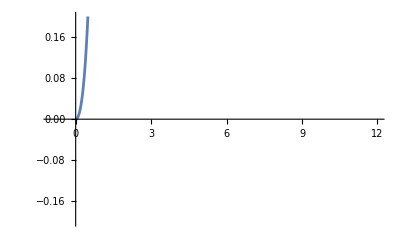
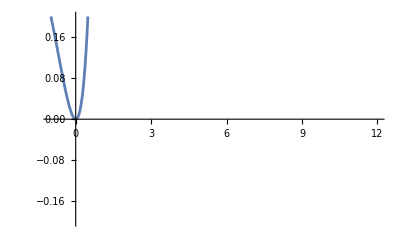
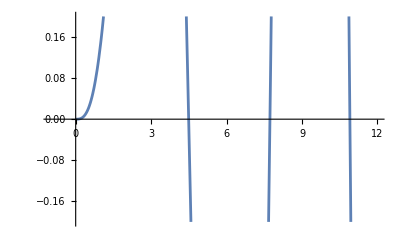
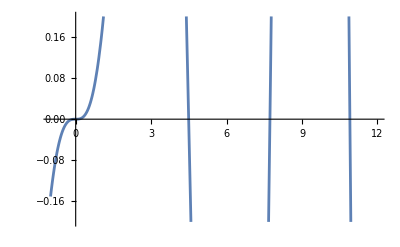
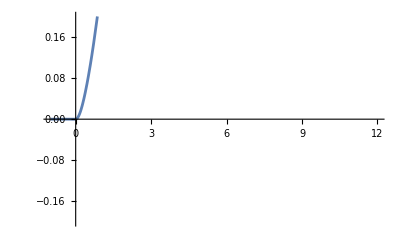
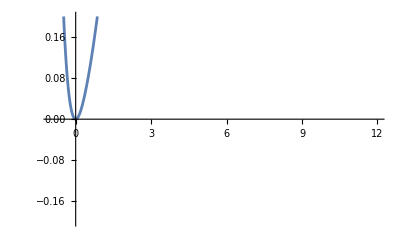
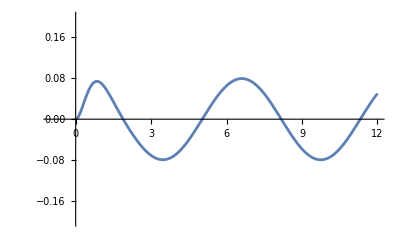
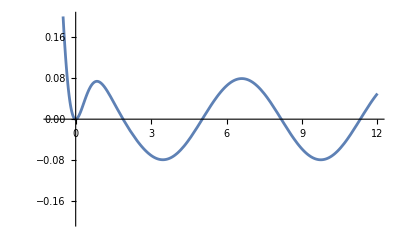
## 6(i) Clear[Derivative] DE=y'[t]-3y[t]== DiracDelta[t] IC={y[0]==0} Gensol = DSolve[{DE, IC}, y, t] Parsol=DSolve[{DE,IC},y,t] DE/. Parsol[[1]]//Simplify y[0]/. Parsol[[1]] y'[0]/. Parsol[[1]] y[t]/. Parsol Simplify[%] TeXForm[%] Plot[y[t]/. Parsol,{t,-1,12},PlotRange->{{-1,12},{-.2,.2}}] -3 y[t]+y'[t]==DiracDelta[t] {y[0]==0} {{y→Function[{t},-ⅇ^(3 t) (HeavisideTheta[0]-HeavisideTheta[t])]}} {{y→Function[{t},-ⅇ^(3 t) (HeavisideTheta[0]-HeavisideTheta[t])]}} True 0 DiracDelta[0] {-ⅇ^(3 t) (HeavisideTheta[0]-HeavisideTheta[t])} {ⅇ^(3 t) (-HeavisideTheta[0]+HeavisideTheta[t])} -Graphics- \left\{e^{3 t} (\theta (t)-\theta (0))\right\} Convolution f[t_]:=Convolve[Exp[3x]*HeavisideTheta[x], Sin[x]*HeavisideTheta[x],x, t] f[t] TeXForm[f[t]] Plot[f[t], {t,-1,12},PlotRange->{{-1,12},{-.2,.2}}] -1/10 HeavisideTheta[t] (-ⅇ^(3 t)+Cos[t]+3 Sin[t]) -Graphics- -\frac{1}{10} \theta (t) \left(-e^{3 t}+3 \sin (t)+\cos (t)\right) Direct Method: Clear[Derivative] DE=y'[t]-3y[t]== Sin[t] IC={y[0]==0} Gensol = DSolve[{DE, IC}, y, t] Parsol=DSolve[{DE,IC},y,t] DE/. Parsol[[1]]//Simplify y[0]/. Parsol[[1]] y'[0]/. Parsol[[1]] y[t]/. Parsol Simplify[%] TeXForm[%] Plot[y[t]/. Parsol,{t,-1,12},PlotRange->{{-1,12},{-.2,.2}}] -3 y[t]+y'[t]==Sin[t] {y[0]==0} {{y→Function[{t},1/10 (ⅇ^(3 t)-Cos[t]-3 Sin[t])]}} {{y→Function[{t},1/10 (ⅇ^(3 t)-Cos[t]-3 Sin[t])]}} True 0 0 {1/10 (ⅇ^(3 t)-Cos[t]-3 Sin[t])} {1/10 (ⅇ^(3 t)-Cos[t]-3 Sin[t])} -Graphics- \left\{\frac{1}{10} \left(e^{3 t}-3 \sin (t)-\cos (t)\right)\right\} 6(ii) Clear[Derivative] DE=y''[t]+y[t]== DiracDelta[t] IC={y[0]==0, y'[0]==0} Gensol = DSolve[{DE, IC}, y, t] Parsol=DSolve[{DE,IC},y,t] DE/. Parsol[[1]]//Simplify y[0]/. Parsol[[1]] y'[0]/. Parsol[[1]] y[t]/. Parsol Simplify[%] TeXForm[%] Plot[y[t]/. Parsol,{t,-1,12},PlotRange->{{-1,12},{-.2,.2}}] y[t]+y''[t]==DiracDelta[t] {y[0]==0,y'[0]==0} {{y→Function[{t},-HeavisideTheta[0] Sin[t]+HeavisideTheta[t] Sin[t]]}} {{y→Function[{t},-HeavisideTheta[0] Sin[t]+HeavisideTheta[t] Sin[t]]}} True 0 0 {-HeavisideTheta[0] Sin[t]+HeavisideTheta[t] Sin[t]} {(-HeavisideTheta[0]+HeavisideTheta[t]) Sin[t]} -Graphics- \{(\theta (t)-\theta (0)) \sin (t)\} f[t_]:=Convolve[Sin[x]*HeavisideTheta[x], Sin[x]*HeavisideTheta[x],x, t] TeXForm[f[t]] Plot[f[t], {t, -1, 12}, PlotRange->{{-1,12},{-.2,.2}}] -Graphics- \frac{1}{2} \theta (t) (\sin (t)-t \cos (t)) Direct Method DE=y''[t]+y[t]== Sin[t] IC={y[0]==0, y'[0]==0} Gensol = DSolve[{DE, IC}, y, t] Parsol=DSolve[{DE,IC},y,t] DE/. Parsol[[1]]//Simplify y[0]/. Parsol[[1]] y'[0]/. Parsol[[1]] y[t]/. Parsol Simplify[%] TeXForm[%] Plot[y[t]/. Parsol,{t,-1,12},PlotRange->{{-1,12},{-.2,.2}}] y[t]+y''[t]==Sin[t] {y[0]==0,y'[0]==0} {{y→Function[{t},1/4 (-2 t Cos[t]+2 Sin[t]-2 Cos[t]^2 Sin[t]+Cos[t] Sin[2 t])]}} {{y→Function[{t},1/4 (-2 t Cos[t]+2 Sin[t]-2 Cos[t]^2 Sin[t]+Cos[t] Sin[2 t])]}} True 0 0 {1/4 (-2 t Cos[t]+2 Sin[t]-2 Cos[t]^2 Sin[t]+Cos[t] Sin[2 t])} {1/2 (-t Cos[t]+Sin[t])} -Graphics- \left\{\frac{1}{2} (\sin (t)-t \cos (t))\right\} 6(iii) Clear[Derivative] DE=y''[t]+4y'[t]+3y[t]== DiracDelta[t] IC={y[0]==0, y'[0]==0} Gensol = DSolve[{DE, IC}, y, t] Parsol=DSolve[{DE,IC},y,t] DE/. Parsol[[1]]//Simplify y[0]/. Parsol[[1]] y'[0]/. Parsol[[1]] y[t]/. Parsol Simplify[%] TeXForm[%] Plot[y[t]/. Parsol,{t,-1,12},PlotRange->{{-1,12},{-.2,.2}}] 3 y[t]+4 y'[t]+y''[t]==DiracDelta[t] {y[0]==0,y'[0]==0} {{y→Function[{t},-1/2 ⅇ^(-3 t) (-1+ⅇ^(2 t)) (HeavisideTheta[0]-HeavisideTheta[t])]}} {{y→Function[{t},-1/2 ⅇ^(-3 t) (-1+ⅇ^(2 t)) (HeavisideTheta[0]-HeavisideTheta[t])]}} 2 ⅇ^(2 t) (DiracDelta[t]/2+3/2 ⅇ^(-3 t) (HeavisideTheta[0]-HeavisideTheta[t]))-3 ⅇ^-t (HeavisideTheta[0]-HeavisideTheta[t])==DiracDelta[t] 0 0 {-1/2 ⅇ^(-3 t) (-1+ⅇ^(2 t)) (HeavisideTheta[0]-HeavisideTheta[t])} {-1/2 ⅇ^(-3 t) (-1+ⅇ^(2 t)) (HeavisideTheta[0]-HeavisideTheta[t])} -Graphics- \left\{-\frac{1}{2} e^{-3 t} \left(e^{2 t}-1\right) (\theta (0)-\theta (t))\right\} Convolution: f[t_]:=Convolve[1/2*(-Exp[-3x]+Exp[-x])*HeavisideTheta[x], Exp[x]*HeavisideTheta[x],x, t] TeXForm[f[t]] Plot[f[t], {t, -1, 12}, PlotRange->{{-1,12},{-.2,.2}}] -Graphics- \frac{1}{2} e^{-t} \theta (t) \sinh ^2(t) Direct Method DE=y''[t]+4y'[t]+3y[t]== Exp[t] IC={y[0]==0, y'[0]==0} Gensol = DSolve[{DE, IC}, y, t] Parsol=DSolve[{DE,IC},y,t] DE/. Parsol[[1]]//Simplify y[0]/. Parsol[[1]] y'[0]/. Parsol[[1]] y[t]/. Parsol Simplify[%] TeXForm[%] Plot[y[t]/. Parsol,{t,-1,12},PlotRange->{{-1,12},{-.2,.2}}] 3 y[t]+4 y'[t]+y''[t]==ⅇ^t {y[0]==0,y'[0]==0} {{y→Function[{t},1/8 ⅇ^(-3 t) (-1+ⅇ^(2 t))^2]}} {{y→Function[{t},1/8 ⅇ^(-3 t) (-1+ⅇ^(2 t))^2]}} True 0 0 {1/8 ⅇ^(-3 t) (-1+ⅇ^(2 t))^2} {1/8 ⅇ^(-3 t) (-1+ⅇ^(2 t))^2} -Graphics- \left\{\frac{1}{8} e^{-3 t} \left(e^{2 t}-1\right)^2\right\} 6(iv) Clear[Derivative] DE=y''[t]+4y'[t]+13y[t]== DiracDelta[t] IC={y[0]==0, y'[0]==0} Gensol = DSolve[{DE, IC}, y, t] Parsol=DSolve[{DE,IC},y,t] DE/. Parsol[[1]]//Simplify y[0]/. Parsol[[1]] y'[0]/. Parsol[[1]] y[t]/. Parsol Simplify[%] TeXForm[%] Plot[y[t]/. Parsol,{t,-1,12},PlotRange->{{-1,12},{-.2,.2}}] 13 y[t]+4 y'[t]+y''[t]==DiracDelta[t] {y[0]==0,y'[0]==0} {{y→Function[{t},-1/3 ⅇ^(-2 t) (HeavisideTheta[0]-HeavisideTheta[t]) Sin[3 t]]}} {{y→Function[{t},-1/3 ⅇ^(-2 t) (HeavisideTheta[0]-HeavisideTheta[t]) Sin[3 t]]}} 3 Cos[3 t] (DiracDelta[t]/3+2/3 ⅇ^(-2 t) (HeavisideTheta[0]-HeavisideTheta[t]))-2 ⅇ^(-2 t) Cos[3 t] (HeavisideTheta[0]-HeavisideTheta[t])==DiracDelta[t] 0 0 {-1/3 ⅇ^(-2 t) (HeavisideTheta[0]-HeavisideTheta[t]) Sin[3 t]} {-1/3 ⅇ^(-2 t) (HeavisideTheta[0]-HeavisideTheta[t]) Sin[3 t]} -Graphics- \left\{-\frac{1}{3} e^{-2 t} (\theta (0)-\theta (t)) \sin (3 t)\right\} Convolution f[t_]:=Convolve[1/3*Exp[-2x]*Sin[3x]*HeavisideTheta[x], Cos[x]*HeavisideTheta[x],x, t] TeXForm[f[t]] Plot[f[t], {t, -1, 12}, PlotRange->{{-1,12},{-.2,.2}}] -Graphics- \frac{1}{120} \theta (t) \left(3 \sin (t)+9 \cos (t)-e^{-2 t} (7 \sin (3 t)+9 \cos (3 t))\right) Direct Method DE=y''[t]+4y'[t]+13y[t]== Cos[t] IC={y[0]==0, y'[0]==0} Gensol = DSolve[{DE, IC}, y, t] Parsol=DSolve[{DE,IC},y,t] DE/. Parsol[[1]]//Simplify y[0]/. Parsol[[1]] y'[0]/. Parsol[[1]] y[t]/. Parsol Simplify[%] TeXForm[%] Plot[y[t]/. Parsol,{t,-1,12},PlotRange->{{-1,12},{-.2,.2}}] 13 y[t]+4 y'[t]+y''[t]==Cos[t] {y[0]==0,y'[0]==0} {{y→Function[{t},1/120 ⅇ^(-2 t) (-9 Cos[3 t]+5 ⅇ^(2 t) Cos[2 t] Cos[3 t]+4 ⅇ^(2 t) Cos[3 t] Cos[4 t]-5 ⅇ^(2 t) Cos[3 t] Sin[2 t]-7 Sin[3 t]+5 ⅇ^(2 t) Cos[2 t] Sin[3 t]+2 ⅇ^(2 t) Cos[4 t] Sin[3 t]+5 ⅇ^(2 t) Sin[2 t] Sin[3 t]-2 ⅇ^(2 t) Cos[3 t] Sin[4 t]+4 ⅇ^(2 t) Sin[3 t] Sin[4 t])]}} {{y→Function[{t},1/120 ⅇ^(-2 t) (-9 Cos[3 t]+5 ⅇ^(2 t) Cos[2 t] Cos[3 t]+4 ⅇ^(2 t) Cos[3 t] Cos[4 t]-5 ⅇ^(2 t) Cos[3 t] Sin[2 t]-7 Sin[3 t]+5 ⅇ^(2 t) Cos[2 t] Sin[3 t]+2 ⅇ^(2 t) Cos[4 t] Sin[3 t]+5 ⅇ^(2 t) Sin[2 t] Sin[3 t]-2 ⅇ^(2 t) Cos[3 t] Sin[4 t]+4 ⅇ^(2 t) Sin[3 t] Sin[4 t])]}} True 0 0 {1/120 ⅇ^(-2 t) (-9 Cos[3 t]+5 ⅇ^(2 t) Cos[2 t] Cos[3 t]+4 ⅇ^(2 t) Cos[3 t] Cos[4 t]-5 ⅇ^(2 t) Cos[3 t] Sin[2 t]-7 Sin[3 t]+5 ⅇ^(2 t) Cos[2 t] Sin[3 t]+2 ⅇ^(2 t) Cos[4 t] Sin[3 t]+5 ⅇ^(2 t) Sin[2 t] Sin[3 t]-2 ⅇ^(2 t) Cos[3 t] Sin[4 t]+4 ⅇ^(2 t) Sin[3 t] Sin[4 t])} {1/120 ⅇ^(-2 t) (9 ⅇ^(2 t) Cos[t]-9 Cos[3 t]+3 ⅇ^(2 t) Sin[t]-7 Sin[3 t])} -Graphics- \left\{\frac{1}{120} e^{-2 t} \left(3 e^{2 t} \sin (t)-7 \sin (3 t)+9 e^{2 t} \cos (t)-9 \cos (3 t)\right)\right\} 7. (i) (f*δ)(t)==∫_0^t f(t-u)δ(u)ⅆu==f(t) (ii) and

## 8. (i) Taking of both sides yields the property. (ii) Taking of both sides yields the property. 8(i) Note that .Differentiating with Leibniz rule gives: 8(ii) Note that Differentiating with Leibniz rule gives: Note that Differentiating again gives 8(iii) Note that and . Upon differentiation, we get , that is, . 8(iv) Note that . Upon differentiation, we get 9(i) Note that .Differentiating with Leibniz rule gives: 9ii) Note that Differentiating with Leibniz rule gives: Note that Differentiating again gives 9(iii) Note that Differentiating yields y''(t)+y(t)==sint. 9(iv) Note that Differentiating gives y''(t)+4y'(t)+4y(t)==0

## 10 (i)

-3 y[t]+y'[t]==DiracDelta[-1+t]

{y[0]==0}

{{y→Function[{t},ⅇ^(-3+3 t) HeavisideTheta[-1+t]]}}

{{y→Function[{t},ⅇ^(-3+3 t) HeavisideTheta[-1+t]]}}

True

0

0

{ⅇ^(-3+3 t) HeavisideTheta[-1+t]}

{ⅇ^(3 (-1+t)) HeavisideTheta[-1+t]}

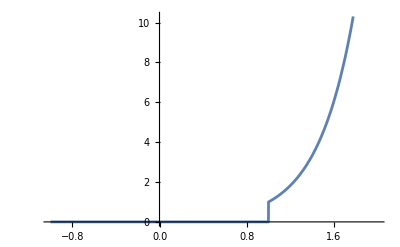

\left\{e^{3 (t-1)} \theta (t-1)\right\}

```mathematica
Clear[Derivative]
DE=y'[t]-3y[t] == DiracDelta[t-1]
IC={y[0]==0}
Gensol = DSolve[{DE, IC}, y, t]
Parsol=DSolve[{DE,IC},y,t]
DE/. Parsol[[1]]//Simplify
y[0]/. Parsol[[1]]
y'[0]/. Parsol[[1]]
y[t]/. Parsol
Simplify[%]
TeXForm[%]
Plot[y[t]/. Parsol,{t,-1,2}]
```

## Using the Convolution-delta theorem

```mathematica
Clear[Derivative]
DE=y'[t]-3y[t] == DiracDelta[t]
IC={y[0]==0}
Gensol = DSolve[{DE, IC}, y, t]
Parsol=DSolve[{DE,IC},y,t]
DE/. Parsol[[1]]//Simplify
y[0]/. Parsol[[1]]
y'[0]/. Parsol[[1]]
y[t]/. Parsol
Simplify[%]
TeXForm[%]
Plot[y[t]/. Parsol,{t,-1,2}]
```

-3 y[t]+y'[t]==DiracDelta[t]

{y[0]==0}

{{y→Function[{t},-ⅇ^(3 t) (HeavisideTheta[0]-HeavisideTheta[t])]}}

{{y→Function[{t},-ⅇ^(3 t) (HeavisideTheta[0]-HeavisideTheta[t])]}}

True

0

DiracDelta[0]

{-ⅇ^(3 t) (HeavisideTheta[0]-HeavisideTheta[t])}

{ⅇ^(3 t) (-HeavisideTheta[0]+HeavisideTheta[t])}

-Graphics-

\left\{e^{3 t} (\theta (t)-\theta (0))\right\}

ⅇ^(-3+3 x) HeavisideTheta[-1+x]

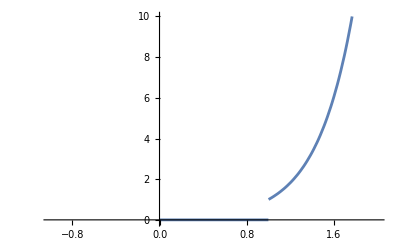

```mathematica
f[x_]:=Convolve[Exp[3t]*HeavisideTheta[t], DiracDelta[t-1]*HeavisideTheta[t], t, x]
f[x]
Plot[f[x], {x, -1, 2}, PlotRange->{{-1, 2},{-0.1, 10}}]
```

## 10 (ii)

4 y[t]+y'[t]==DiracDelta[-2+t]

{y[0]==1}

{{y→Function[{t},ⅇ^(-4 t) (1+ⅇ^8 HeavisideTheta[-2+t])]}}

{{y→Function[{t},ⅇ^(-4 t) (1+ⅇ^8 HeavisideTheta[-2+t])]}}

True

1

-4

{ⅇ^(-4 t) (1+ⅇ^8 HeavisideTheta[-2+t])}

{ⅇ^(-4 t) (1+ⅇ^8 HeavisideTheta[-2+t])}

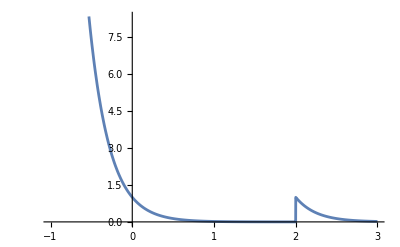

\left\{e^{-4 t} \left(e^8 \theta (t-2)+1\right)\right\}

```mathematica
Clear[Derivative]
DE=y'[t]+4y[t] == DiracDelta[t-2]
IC={y[0]==1}
Gensol = DSolve[{DE, IC}, y, t]
Parsol=DSolve[{DE,IC},y,t]
DE/. Parsol[[1]]//Simplify
y[0]/. Parsol[[1]]
y'[0]/. Parsol[[1]]
y[t]/. Parsol
Simplify[%]
TeXForm[%]
Plot[y[t]/. Parsol,{t,-1,3}]
```

## 10 (iii)

4 y[t]+y''[t]==DiracDelta[-2 π+t]

{y[0]==0,y'[0]==0}

{{y→Function[{t},1/2 HeavisideTheta[-2 π+t] Sin[2 t]]}}

{{y→Function[{t},1/2 HeavisideTheta[-2 π+t] Sin[2 t]]}}

True

0

0

{1/2 HeavisideTheta[-2 π+t] Sin[2 t]}

{Cos[t] HeavisideTheta[-2 π+t] Sin[t]}

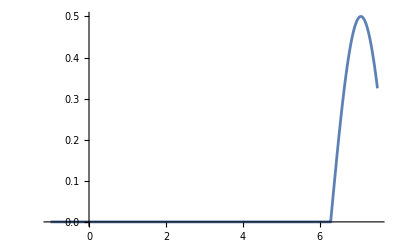

\{\theta (t-2 \pi ) \sin (t) \cos (t)\}

```mathematica
Clear[Derivative]
DE=y''[t]+4*y[t] == DiracDelta[t-2*Pi]
IC={y[0]==0, y'[0]==0}
Gensol = DSolve[{DE, IC}, y, t]
Parsol=DSolve[{DE,IC},y,t]
DE/. Parsol[[1]]//Simplify
y[0]/. Parsol[[1]]
y'[0]/. Parsol[[1]]
y[t]/. Parsol
Simplify[%]
TeXForm[%]
Plot[y[t]/. Parsol,{t,-1,7.5}]
```

## 10(iv)

3 y[t]+4 y'[t]+y''[t]==DiracDelta[-2 π+t]

{y[0]==0,y'[0]==0}

{{y→Function[{t},1/2 ⅇ^(2 π-3 t) (-ⅇ^(4 π)+ⅇ^(2 t)) HeavisideTheta[-2 π+t]]}}

{{y→Function[{t},1/2 ⅇ^(2 π-3 t) (-ⅇ^(4 π)+ⅇ^(2 t)) HeavisideTheta[-2 π+t]]}}

3 ⅇ^(2 π-t) HeavisideTheta[-2 π+t]+2 ⅇ^(2 t) (1/2 ⅇ^(-4 π) DiracDelta[-2 π+t]-3/2 ⅇ^(2 π-3 t) HeavisideTheta[-2 π+t])==DiracDelta[-2 π+t]

0

0

{1/2 ⅇ^(2 π-3 t) (-ⅇ^(4 π)+ⅇ^(2 t)) HeavisideTheta[-2 π+t]}

{1/2 ⅇ^(2 π-3 t) (-ⅇ^(4 π)+ⅇ^(2 t)) HeavisideTheta[-2 π+t]}

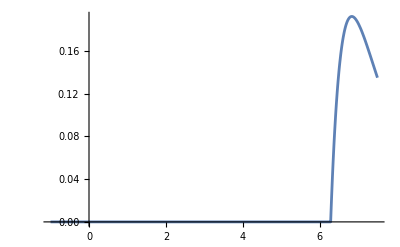

\left\{\frac{1}{2} e^{2 \pi -3 t} \left(e^{2 t}-e^{4 \pi }\right) \theta (t-2 \pi )\right\}

```mathematica
Clear[Derivative]
DE=y''[t]+4*y'[t]+3y[t] == DiracDelta[t-2*Pi]
IC={y[0]==0, y'[0]==0}
Gensol = DSolve[{DE, IC}, y, t]
Parsol=DSolve[{DE,IC},y,t]
DE/. Parsol[[1]]//Simplify
y[0]/. Parsol[[1]]
y'[0]/. Parsol[[1]]
y[t]/. Parsol
Simplify[%]
TeXForm[%]
Plot[y[t]/. Parsol,{t,-1,7.5}]
```

## 10(v)

13 y[t]+4 y'[t]+y''[t]==DiracDelta[-2 π+t]

{y[0]==0,y'[0]==0}

{{y→Function[{t},1/3 ⅇ^(4 π-2 t) HeavisideTheta[-2 π+t] Sin[3 t]]}}

{{y→Function[{t},1/3 ⅇ^(4 π-2 t) HeavisideTheta[-2 π+t] Sin[3 t]]}}

2 ⅇ^(4 π-2 t) Cos[3 t] HeavisideTheta[-2 π+t]+3 Cos[3 t] (1/3 DiracDelta[-2 π+t]-2/3 ⅇ^(4 π-2 t) HeavisideTheta[-2 π+t])==DiracDelta[-2 π+t]

0

0

{1/3 ⅇ^(4 π-2 t) HeavisideTheta[-2 π+t] Sin[3 t]}

{1/3 ⅇ^(4 π-2 t) HeavisideTheta[-2 π+t] Sin[3 t]}

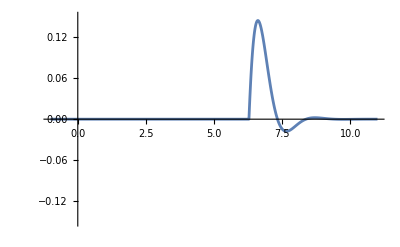

\left\{\frac{1}{3} e^{4 \pi -2 t} \theta (t-2 \pi ) \sin (3 t)\right\}

```mathematica
Clear[Derivative]
DE=y''[t]+4*y'[t]+13y[t] ==DiracDelta[t-2*Pi]
IC={y[0]==0, y'[0]==0}
Gensol = DSolve[{DE, IC}, y, t]
Parsol=DSolve[{DE,IC},y,t]
DE/. Parsol[[1]]//Simplify
y[0]/. Parsol[[1]]
y'[0]/. Parsol[[1]]
y[t]/. Parsol
Simplify[%]
TeXForm[%]
Plot[y[t]/. Parsol,{t,-1,11},PlotRange->{{-1, 11},{-0.15,.15}}]
```

## 10 (vi)

3 y[t]+4 y'[t]+y''[t]==DiracDelta[-3 π+t]+DiracDelta[-2 π+t]

{y[0]==0,y'[0]==0}

{{y→Function[{t},1/2 ⅇ^(2 π-3 t) (-ⅇ^(7 π) HeavisideTheta[-3 π+t]+ⅇ^(π+2 t) HeavisideTheta[-3 π+t]-ⅇ^(4 π) HeavisideTheta[-2 π+t]+ⅇ^(2 t) HeavisideTheta[-2 π+t])]}}

{{y→Function[{t},1/2 ⅇ^(2 π-3 t) (-ⅇ^(7 π) HeavisideTheta[-3 π+t]+ⅇ^(π+2 t) HeavisideTheta[-3 π+t]-ⅇ^(4 π) HeavisideTheta[-2 π+t]+ⅇ^(2 t) HeavisideTheta[-2 π+t])]}}

-2 ⅇ^(2 π-t) (ⅇ^π HeavisideTheta[-3 π+t]+HeavisideTheta[-2 π+t])+1/2 ⅇ^(2 π-3 t) (2 ⅇ^(7 π) DiracDelta[-3 π+t]+2 ⅇ^(4 π) DiracDelta[-2 π+t]+4 ⅇ^(2 t) (ⅇ^π HeavisideTheta[-3 π+t]+HeavisideTheta[-2 π+t]))==DiracDelta[-3 π+t]+DiracDelta[-2 π+t]

0

0

{1/2 ⅇ^(2 π-3 t) (-ⅇ^(7 π) HeavisideTheta[-3 π+t]+ⅇ^(π+2 t) HeavisideTheta[-3 π+t]-ⅇ^(4 π) HeavisideTheta[-2 π+t]+ⅇ^(2 t) HeavisideTheta[-2 π+t])}

{1/2 ⅇ^(2 π-3 t) ((-ⅇ^(7 π)+ⅇ^(π+2 t)) HeavisideTheta[-3 π+t]-(ⅇ^(4 π)-ⅇ^(2 t)) HeavisideTheta[-2 π+t])}

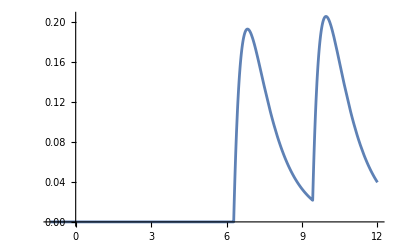

\left\{\frac{1}{2} e^{2 \pi -3 t} \left(\left(e^{2 t+\pi }-e^{7 \pi }\right) \theta (t-3 \pi )-\left(e^{4 \pi }-e^{2 t}\right) \theta (t-2 \pi )\right)\right\}

```mathematica
Clear[Derivative]
DE=y''[t]+4*y'[t]+3y[t] == DiracDelta[t-2*Pi]+DiracDelta[t-3*Pi]
IC={y[0]==0, y'[0]==0}
Gensol = DSolve[{DE, IC}, y, t]
Parsol=DSolve[{DE,IC},y,t]
DE/. Parsol[[1]]//Simplify
y[0]/. Parsol[[1]]
y'[0]/. Parsol[[1]]
y[t]/. Parsol
Simplify[%]
TeXForm[%]
Plot[y[t]/. Parsol,{t,-1,12}]
```

## 10(vii)

13 y[t]+4 y'[t]+y''[t]==DiracDelta[-2 π+t]+DiracDelta[-π+t]

{y[0]==0,y'[0]==0}

{{y→Function[{t},1/3 ⅇ^(2 π-2 t) (ⅇ^(2 π) HeavisideTheta[-2 π+t]-HeavisideTheta[-π+t]) Sin[3 t]]}}

{{y→Function[{t},1/3 ⅇ^(2 π-2 t) (ⅇ^(2 π) HeavisideTheta[-2 π+t]-HeavisideTheta[-π+t]) Sin[3 t]]}}

3 Cos[3 t] (1/3 ⅇ^(2 π-2 t) (ⅇ^(2 π) DiracDelta[-2 π+t]-DiracDelta[-π+t])-2/3 ⅇ^(2 π-2 t) (ⅇ^(2 π) HeavisideTheta[-2 π+t]-HeavisideTheta[-π+t]))+1/3 ⅇ^(2 π-2 t) (ⅇ^(2 π) DiracDelta[-2 π+t]-DiracDelta[-π+t]) (3 Cos[3 t]-2 Sin[3 t])+8/3 ⅇ^(2 π-2 t) (ⅇ^(2 π) HeavisideTheta[-2 π+t]-HeavisideTheta[-π+t]) Sin[3 t]-2 ⅇ^(2 π-2 t) (Cos[3 t] (ⅇ^(2 π) HeavisideTheta[-2 π+t]-HeavisideTheta[-π+t])+1/3 (ⅇ^(2 π) DiracDelta[-2 π+t]-DiracDelta[-π+t]) Sin[3 t])+4 (1/3 ⅇ^(2 π-2 t) (ⅇ^(2 π) HeavisideTheta[-2 π+t]-HeavisideTheta[-π+t]) (3 Cos[3 t]-2 Sin[3 t])+1/3 ⅇ^(2 π-2 t) (ⅇ^(2 π) DiracDelta[-2 π+t]-DiracDelta[-π+t]) Sin[3 t])+1/3 ⅇ^(2 π-2 t) Sin[3 t] (ⅇ^(2 π) DiracDelta'[-2 π+t]-DiracDelta'[-π+t])==DiracDelta[-2 π+t]+DiracDelta[-π+t]

0

0

{1/3 ⅇ^(2 π-2 t) (ⅇ^(2 π) HeavisideTheta[-2 π+t]-HeavisideTheta[-π+t]) Sin[3 t]}

{1/3 ⅇ^(2 π-2 t) (ⅇ^(2 π) HeavisideTheta[-2 π+t]-HeavisideTheta[-π+t]) Sin[3 t]}

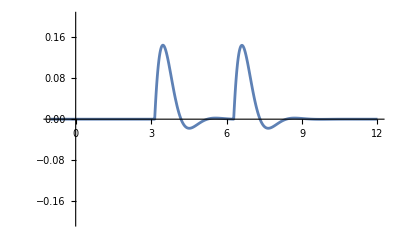

\left\{\frac{1}{3} e^{2 \pi -2 t} \left(e^{2 \pi } \theta (t-2 \pi )-\theta (t-\pi )\right) \sin (3 t)\right\}

```mathematica
Clear[Derivative]
DE=y''[t]+4*y'[t]+13y[t] == DiracDelta[t-Pi]+DiracDelta[t-2Pi]
IC={y[0]==0, y'[0]==0}
Gensol = DSolve[{DE, IC}, y, t]
Parsol=DSolve[{DE,IC},y,t]
DE/. Parsol[[1]]//Simplify
y[0]/. Parsol[[1]]
y'[0]/. Parsol[[1]]
y[t]/. Parsol
Simplify[%]
TeXForm[%]
Plot[y[t]/. Parsol,{t,-1,12},PlotRange->{{-1,12},{-.2,.2}}]
```

## 11(i)

4 y[t]+y''[t]==0

{y[0]==1,y'[0]==0}

{{y→Function[{t},Cos[2 t]]}}

{{y→Function[{t},Cos[2 t]]}}

True

1

0

{Cos[2 t]}

{Cos[2 t]}

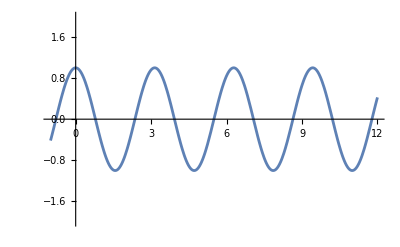

\{\cos (2 t)\}

```mathematica
DE=y''[t]+4y[t]== 0
IC={y[0]==1, y'[0]==0}
Gensol = DSolve[{DE, IC}, y, t]
Parsol=DSolve[{DE,IC},y,t]
DE/. Parsol[[1]]//Simplify
y[0]/. Parsol[[1]]
y'[0]/. Parsol[[1]]
y[t]/. Parsol
Simplify[%]
TeXForm[%]
Plot[y[t]/. Parsol,{t,-1,12},PlotRange->{{-1,12},{-2,2}}]
```

```mathematica
Solve[cos[2t]==0, t]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

```mathematica
{{t->1/2 (cos^(-1))[0]}}
y[Pi/4]/.Parsol
y'[Pi/4]/.Parsol
```

{{t→1/2 cos^(-1)[0]}}

{0}

{-2 (1-HeavisideTheta[0])}

## 11(i)

4 y[t]+y''[t]==8 DiracDelta[-π+4 t]

{y[0]==1,y'[0]==0}

{{y→Function[{t},-Cos[2 t] (-1+HeavisideTheta[-π+4 t])]}}

{{y→Function[{t},-Cos[2 t] (-1+HeavisideTheta[-π+4 t])]}}

True

1

0

{-Cos[2 t] (-1+HeavisideTheta[-π+4 t])}

{-Cos[2 t] (-1+HeavisideTheta[-π+4 t])}

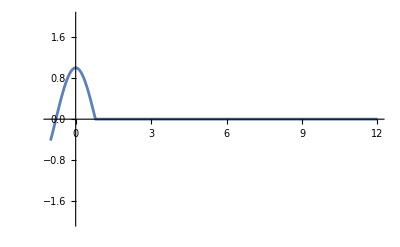

\{(\theta (4 t-\pi )-1) (-\cos (2 t))\}

```mathematica
DE=y''[t]+4y[t]== 2DiracDelta[t-Pi/4]
IC={y[0]==1, y'[0]==0}
Gensol = DSolve[{DE, IC}, y, t]
Parsol=DSolve[{DE,IC},y,t]
DE/. Parsol[[1]]//Simplify
y[0]/. Parsol[[1]]
y'[0]/. Parsol[[1]]
y[t]/. Parsol
Simplify[%]
TeXForm[%]
Plot[y[t]/. Parsol,{t,-1,12},PlotRange->{{-1,12},{-2,2}}]
```

## 11(iii)

4 y[t]+y''[t]==-8 DiracDelta[-3 π+4 t]

{y[0]==1,y'[0]==0}

{{y→Function[{t},-Cos[2 t] (-1+HeavisideTheta[-3 π+4 t])]}}

{{y→Function[{t},-Cos[2 t] (-1+HeavisideTheta[-3 π+4 t])]}}

-8 DiracDelta[3 π-4 t]==-8 DiracDelta[-3 π+4 t]

1

0

{-Cos[2 t] (-1+HeavisideTheta[-3 π+4 t])}

{-Cos[2 t] (-1+HeavisideTheta[-3 π+4 t])}

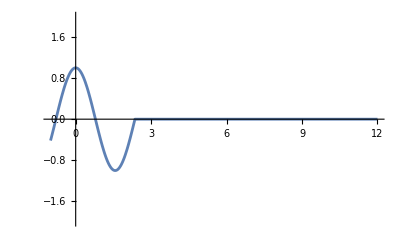

\{(\theta (4 t-3 \pi )-1) (-\cos (2 t))\}

```mathematica
DE=y''[t]+4y[t]== -2DiracDelta[t-3Pi/4]
IC={y[0]==1, y'[0]==0}
Gensol = DSolve[{DE, IC}, y, t]
Parsol=DSolve[{DE,IC},y,t]
DE/. Parsol[[1]]//Simplify
y[0]/. Parsol[[1]]
y'[0]/. Parsol[[1]]
y[t]/. Parsol
Simplify[%]
TeXForm[%]
Plot[y[t]/. Parsol,{t,-1,12},PlotRange->{{-1,12},{-2,2}}]
```